## Pre-calculus Exponents & Logarithms Sketch the graph of f

### f(x) = 2^x

```mathematica
Plot[2^x, {x, -5, 5}]
```

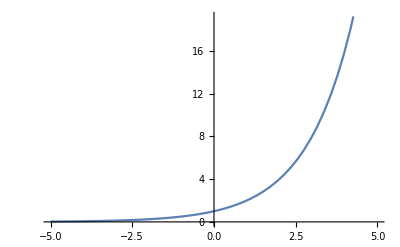

### f(x) = -3^x

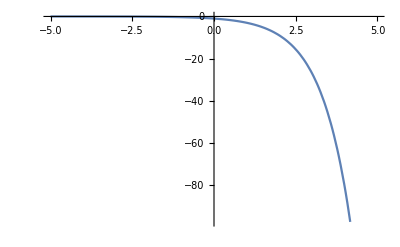

```mathematica
Plot[-3^x,{x, -5, 5}]
```

### f(x) = 2(5)^x

```mathematica
Plot[2(5)^x, {x, -5, 5}]
```

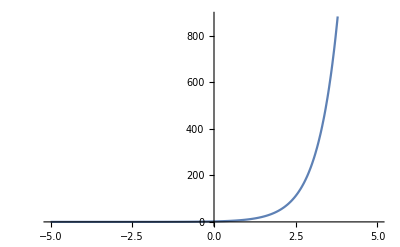

### f(x) = 7^x+ 3

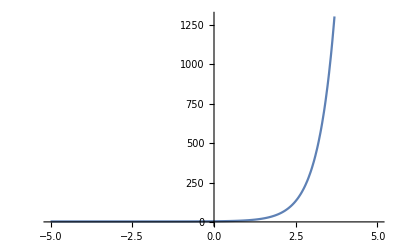

```mathematica
Plot[7^x+3, {x, -5, 5}]
```

### f(x) = 4^-x

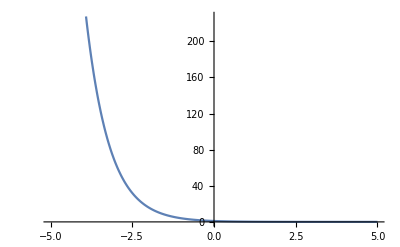

```mathematica
Plot[4^-x, {x, -5, 5}]
```

### f(x) = (1/2)^x

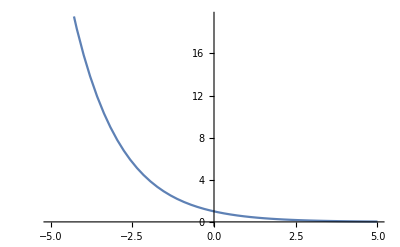

```mathematica
Plot[(1/2)^x, {x, -5, 5}]
```

## Solve the equations

### 5^(x + 8) = 5^(3x - 2)

5^(x + 8) = 5^(3x  -  2)
x + 8 = 3x - 2
x-3x = -2 -8
-2x = -10
2x = 10
x = 5

```mathematica
Solve[5^(x + 8) == 5^(3x - 2), x, Reals]
```

{{x→5}}

### 8^(7 - x)=8^(2x + 1)

8^(7 - x)=8^(2x + 1)
7 - x = 2x + 1
6 = 3x
x = 2

```mathematica
Solve[8^(7-x)==8^(2x+1), x, Reals]
```

{{x→2}}

### 5^(x^2)=5^(2x + 3)

5^(x^2)=5^(2x+3)
x^2=2x+3
x^2- 2x - 3 = 0
(x+1)(x-3) = 0
x_1= -1,  x_2= 3

```mathematica
Solve[5^(x^2)==5^(2x+3), x, Reals]
```

{{x→-1},{x→3}}

### 25^(x^2)= 5^(3x + 2)

5^(2 x^2)= 5^(3x + 2)
2 x^2 = 3x + 2
2 x^2 - 3x - 2 = 0
 I wasn't  sure how to factor it, so just used Mathematica to factor.
(x - 2) (2 x + 1) == 0
x_1= 2,  x_2= -1/2

```mathematica
Solve[25^(x^2)== 5^(3x + 2), x, Reals]
```

{{x→-1/2},{x→2}}

## Solve word problems

### A colony of an endangered species originally numbered 1,000 was predicted to have a population N after t years given by the equation N(t) = 1000(0.9)^t. Estimate population after: a) 1 year b) 5 years c) 10 years

```mathematica
1000(0.9)^1
1000(0.9)^5
1000(0.9)^10
```

900.

590.49

348.678

### The number of bacteria in a certain culture increased from 600 to 1800 between 8 am and 10 am. Assuming the growth is exponential, the number f(t) of bacteria t hours after 8 am is given by f(t) = 600(3)^(t/2). a) Estimate the number of bacteria at 9 am, 11 am, and noon. b) Sketch the graph of f

1039.23

3117.69

5400

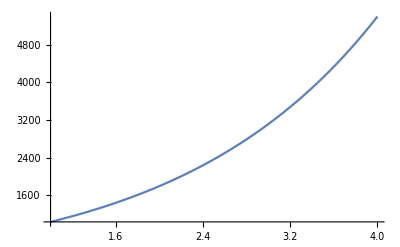

```mathematica
600 (3)^(1/2)// N
600(3)^(3/2)//N
600 (3)^2
Plot[600(3)^(t/2), {t, 1, 4}]
```

### An important problem in oceanography is to determine the amount of light that can penetrate to various ocean depths. The Beer - Lambert law asserts that the exponential function given by I(x) = I_0 c^x is a model for this phenomenon. For a certain location, I(x) = 10(0.4)^x is the amount of light (in calories/cm^2/sec) reaching a depth of x meters. a) Find the amount of light at a depth of 2 m. b) Sketch the graph of I for 0 ≤ x ≤ 5.

1.6

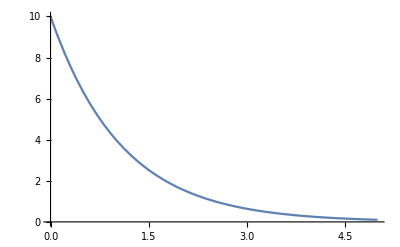

```mathematica
10(0.4)^2
Plot[10(0.4)^x, {x, 0, 5} ]
```